# Simple Task 4

Brian Carlson 2-7-14

## Problem 1.

```mathematica
addPrimes[startInput_,target_]:= Module[
{list1={},sum = 0},
For[ start = startInput,sum < target, 
,sum += Prime[start];
start ++ 
]; 

Return[{sum, Prime[start-1]}]
]
```

```mathematica
addPrimes[13,253]
```

{304,61}

```mathematica
addPrimes[1, 30]
```

{41,13}

```mathematica
2+ 3+5+7+11+13
```

41

## Problem 2.

```mathematica
separateNonlist[list_]:= Module[
{list1 = {},i=1},
While[i ≤ Length[list],
If[ListQ[list[[i]]]== False,
AppendTo[list1,list[[i]]];
];
i++;
];
Return[list1]
]
```

```mathematica
lst={4.2, {3,2}, 3 + i 5, 8.888, √2 , {{1,2}, {3, 2, 5}}, "hi there", goToppers}
```

{4.2,{3,2},3+5 i,8.888,√2,{{1,2},{3,2,5}},hi there,goToppers}

```mathematica
separateNonlist[lst]
```

{4.2,3+5 i,8.888,√2,hi there,goToppers}

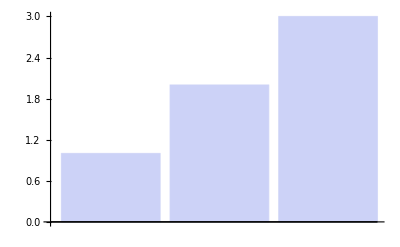
{-Graphics3D-,{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},2.3,16,{flsj,eojnf,ojef},,I like tacos!,-Graphics-,}

```mathematica
otherList = {Graphics3D[Sphere[],ImageSize->60],Table[Mouseover[ArrayPlot[CellularAutomaton[n,{{1},0},{10,All}],ImageSize->50],n,Alignment->Center,ImageSize->All],{n,64}],2.3,4^2,{flsj,eojnf,ojef}, 
Animate[Plot3D[Sin[Cos[Tan[c*x]]]*Sin[Cos[Tan[d*y]]],{x,-50,50},{y,-50,50}],{c,-20,20},{d,-20,20},AnimationRunning->False]
,"I like tacos!",
Tooltip[BarChart[Button[#,Speak[#]]&/@{1,2,3}],"The graph is speaking!"],Hyperlink[Tooltip[-Graphics-,"It's a banana! Click me."],"http://www.youtube.com/watch?v=LH5ay10RTGY"]}
```

```mathematica
separateNonlist[otherList]
```

{-Graphics3D-,2.3,16,,I like tacos!,-Graphics-,}